# Mathematica Bootcamp: Step 3

전경원 박사

Machine Learning Research Engineer
(주)시정
ruddyscent@gmail.com

2021년 10월 18일 월요일

## Access to Lecture Materials

최신 자료는 아래 링크에서 내려받으실 수 있습니다.

https://github.com/ruddyscent/mathematica-bootcamp-2021

## References

체험하며 배우는 WOLFRAM MATHEMATICA
-Graphics-

Wolfram 언어 기초 입문
-Graphics-

Hands-on Start to Mathematica Online, Wolfram U
https://www.wolfram.com/wolfram-u/hands-on-start-to-mathematica-online/

## Wolfram Language

## Syntax Coloring

```mathematica
Expand[(x+1)^10]
```

Expandd[(x+1)^10]

Expand[

Expand[]]

```mathematica
Range[2,12,3]
```

Range[]

Range[2,12,3,1]

## 참값과 근삿값

718을 3으로 나눈값은?

```mathematica
718/3
```

718을 3으로 나누었을 때의 근삿값은?

```mathematica
N[718/3]
```

## List

```mathematica
{1,a,"가나다",-Graphics-,{}}
```

## 1부터 10까지의 자연수

```mathematica
{1,2,3,4,5,6,7,8,9,10}
```

Range[10]

Range[1, 10]

Range[1, 10, 3]

## 1부터 100까지 제곱수의 목록

```mathematica
{1^2,2^2,3^2,4^2,5^2,6^2,7^2,8^2,9^2,10^2}
```

Table[i^2,{i,10}]

Table[i^2,{i,0,10}]

Table[i^2,{i,0,10,2}]

Table[{i,i^2},{i,10}]

Table[π,10]

## 함수

```mathematica
f[x]
```

Sin[π]

전위 형식

```mathematica
f@x
```

Sin@π

후위 형식

```mathematica
x//f
```

π//Sin

## 합성함수.1c

```mathematica
g[f[x]]
```

Sin[Sin[π]]

전위 형식

```mathematica
g@f@x
```

Sin@Sin@π

후위 형식

```mathematica
x//f//g
```

x // Sin // Sin

## 순수함수

```mathematica
#^2&
```

Evaluate

```mathematica
#^2&[2]
```

전위 형식

```mathematica
#^2&@2
```

후위 형식

```mathematica
2//#^2&
```

## Rule

```mathematica
x->2
```

x^2/.x→2

Table[(x+i)^2,{i,10}]
%/.x→0

{f[x],g[x]}
%/.{f→(#^2&),g→(Sin[#]&)}

## Algebraic Manipulation

## 기본 연산

상쇄

```mathematica
(2 a b)/(b c)
```

전개

```mathematica
(a+b)(a+c)(b+c)
```

Expand[(a+b)(a+c)(b+c)]

a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2

인수분해

```mathematica
a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2
```

Factor[a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2]

(a+b) (a+c) (b+c)

## 분수

통분

```mathematica
1/(x+1)+1/(x-1)
```

Together[1/(x+1)+1/(x-1)]

분수 분해

```mathematica
(2 x)/((-1+x) (1+x))
```

Apart[(2 x)/((-1+x) (1+x))]

항의 정리

```mathematica
a x^2+b x^2+c x y
```

Collect[a x^2+b x^2 y+c x y^2,x]

Collect[a x^2+b x^2 y+c x y^2,y]

## 삼각함수

수식 정리

```mathematica
Sin[x]^2+Cos[x]^2
```

Cos[x]^2+Sin[x]^2

Sin[x]^2+Cos[x]^2//Simplify

1

```mathematica
Simplify[√(x^2)]
```

√(x^2)

Simplify[√(x^2),x>0]

x

삼각함수의 조작

```mathematica
Sin[x^2]+Cos[2 x]
```

TrigExpand[Sin[x^2]+Cos[2 x]]

TrigReduce[Cos[x]^2-Sin[x]^2+Sin[x^2]]

Cos[x]^2-Sin[x]^2+Sin[x^2]//Simplify

## 방정식의 풀이

방정식의 풀이

```mathematica
x^2+2x-1==0
```

Solve[x^2+2x-1==0,x]

연립방정식의 풀이

```mathematica
{2x+y==12,x+4y==34}
```

Solve[{2x+y==12,x+4y==34},{x,y}]

일반적 풀이 구하기

```mathematica
Solve[x^2-y^3==1,{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→-√(1+y^3)},{x→√(1+y^3)}}

Reduce[x^2-y^3==1,{x,y}]

수치해 구하기

```mathematica
Sin[x^2]-Cos[x]==0
```

Plot[Sin[x^2]-Cos[x],{x,0,10}]

Solve[Sin[x^2]-Cos[x]==0,x]
%/.C[1]→-1//N

FindRoot[Sin[x^2]-Cos[x],{x,π}]

```mathematica
x+ⅇ^x==1/2
```

ⅇ^x+x==1/2

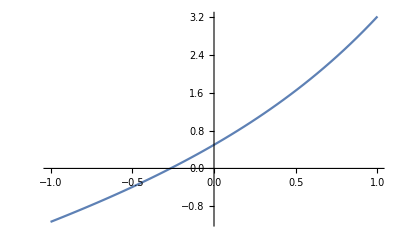

```mathematica
Plot[x+ⅇ^x-1/2,{x,-1,1}]
```

```mathematica
Solve[x+ⅇ^x==1/2,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/2 (1-2 ProductLog[√ⅇ])}}

```mathematica
Reduce[x+ⅇ^x==1/2,x]
%/.C[1]->0
%//N
```

C[1]∈ℤ&&x==1/2-ProductLog[C[1],√ⅇ]

x==1/2-ProductLog[√ⅇ]

x==-0.266249

```mathematica
FindRoot[x+ⅇ^x-1/2,{x,0}]
```

{x→-0.266249}